```mathematica
af=Import["G:\\calc-online\\gpd\\k-result\\diagram-f-n.wdx"];
f1f=Query[1,1]@af;
g1f=Query[1,2]@af;
f2f=Query[2,1]@af;
g2f=Query[2,2]@af;
f3f=Query[3,1]@af;
g3f=Query[3,2]@af;
f12f=f1f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f22f=f2f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f32f=f3f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g12f=g1f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g22f=g2f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g32f=g3f/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};

ft1f=f12f/.{Q^2->(-t),Q^4->t^2};
ft2f=f22f/.{Q^2->(-t),Q^4->t^2};
ft3f=f32f/.{Q^2->(-t),Q^4->t^2};
gt1f=g12f/.{Q^2->(-t),Q^4->t^2};
gt2f=g22f/.{Q^2->(-t),Q^4->t^2};
gt3f=g32f/.{Q^2->(-t),Q^4->t^2};
```

```mathematica
nf1f[y_]=Simplify[ft1f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng1f[y_]=Simplify[gt1f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
nf2f[y_]=Simplify[ft2f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng2f[y_]=Simplify[gt2f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
nf3f=Simplify[ft3f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng3f=Simplify[gt3f/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
```

```mathematica
inf1f[y_]:=NIntegrate[nf1f[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
inf2f[y_]:=NIntegrate[nf2f[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1f[y_]:=NIntegrate[ng1f[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing2f[y_]:=NIntegrate[ng2f[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lf1f=ParallelTable[{y,inf1f[y]},{y,-0.2,0,0.02}];
lf2f=ParallelTable[{y,inf2f[y]},{y,0,0.9,0.02}];
lg1f=ParallelTable[{y,ing1f[y]},{y,-0.2,0,0.02}];
lg2f=ParallelTable[{y,ing2f[y]},{y,0,0.9,0.02}];
```

```mathematica
sf1f=Interpolation[lf1f];
sf2f=Interpolation[lf2f];
sg1f=Interpolation[lg1f];
sg2f=Interpolation[lg2f];
```

```mathematica
(*分成几段，小于0的只有f图，这样*)
```

```mathematica
cf1[x_]=sf1f[x];
cf2[x_]=sf2f[x]-sf1[x];
cf3[x_]=sf2f[x]-sf2[x];
cf4[x_]=-sf2[x];
```

```mathematica
cf1[0]
```

0.-100.102 ⅈ

```mathematica
cf2[0]
```

0.-101.637 ⅈ

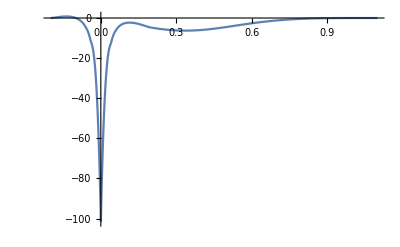

```mathematica
Show[Plot[(-I)*cf1[x],{x,-0.2,0},PlotRange->{{-0.2,1.1},All}],Plot[(-I)*cf2[x],{x,0,0.2},PlotRange->{{-0.1,1},All}],Plot[(-I)*cf3[x],{x,0.2,0.9},PlotRange->{{-0.1,1},All}],Plot[(-I)*cf4[x],{x,0.9,1.1},PlotRange->{{-0.1,1},All}]]
```

```mathematica
path0=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f+g-f-xi1.pdf"}];
Export[path0,Labeled[Show[Plot[(-I)*cf1[x],{x,-0.2,0},PlotRange->{{-0.2,1.1},All}],Plot[(-I)*cf2[x],{x,0,0.2},PlotRange->{{-0.1,1},All}],Plot[(-I)*cf3[x],{x,0.2,0.9},PlotRange->{{-0.1,1},All}],Plot[(-I)*cf4[x],{x,0.9,1.1},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,f+g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f+g-f-xi1.pdf

```mathematica
cg1[x_]=sg1f[x];
cg2[x_]=sg2f[x]-sg1[x];
cg3[x_]=sg2f[x]-sg2[x];
cg4[x_]=-sg2[x];
```

```mathematica
path01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f+g-g-xi1.pdf"}];
Export[path01,Labeled[Show[Plot[(-I)*cg1[x],{x,-0.2,0},PlotRange->{{-0.2,1.1},All}],Plot[(-I)*cg2[x],{x,0,0.2},PlotRange->{{-0.1,1},All}],Plot[(-I)*cg3[x],{x,0.2,0.9},PlotRange->{{-0.1,1},All}],Plot[(-I)*cg4[x],{x,0.9,1.1},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,f+g],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f+g-g-xi1.pdf

```mathematica
cg1[0]
```

0.+75.5929 ⅈ

```mathematica
cg2[0]
```

0.-76.3755 ⅈ

```mathematica
sg1[0]
```

0.+75.9842 ⅈ

```mathematica
sg1f[0]
```

0.+75.5929 ⅈ

```mathematica
sf1f[0]
```

0.-100.102 ⅈ

```mathematica
sf1[0]
```

0.+100.814 ⅈ

```mathematica
NIntegrate[I*sg1[x],{x,0,0.2}]+NIntegrate[I*sg2[x],{x,0.2,1.1}]
```

-2.98209+0. ⅈ

```mathematica
NIntegrate[-I*sg1f[x],{x,-0.2,0}]+NIntegrate[-I*sg2f[x],{x,0,0.9}]
```

-1.81406+0. ⅈ